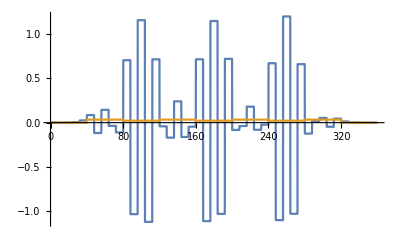

```mathematica
flux=Import["G:\\My Drive\\WN23\\561 Core Des\\HW\\9\\phi-360-2.txt","Table"];
interp=TimeSeries[
flux[[All,2]],
{flux[[All,1]]},
ResamplingMethod->{
"Interpolation",
InterpolationOrder->0
}
];source=Import["G:\\My Drive\\WN23\\561 Core Des\\HW\\9\\source-360-2.txt","Table"];
sint=TimeSeries[
source[[All,2]],
{source[[All,1]]},
ResamplingMethod->{
"Interpolation",
InterpolationOrder->0
}
];
Plot[{interp[x],sint[x]},{x,0,360},PlotRange->All]
```